```mathematica
loglikelihood[x_, theta_] := Log[theta * x + (1 - theta) * (1 - x)]
```

```mathematica
D[loglikelihood[x, theta], theta]
```

(-1+2 x)/((1-theta) (1-x)+theta x)

```mathematica
score[xStar_, thetaStar_] := D[loglikelihood[x, theta], theta]/.{x->xStar,theta->thetaStar}
```

```mathematica
score[1, 0.5]
```

2.

```mathematica
heads=1
```

1

```mathematica
tails = 0
```

0

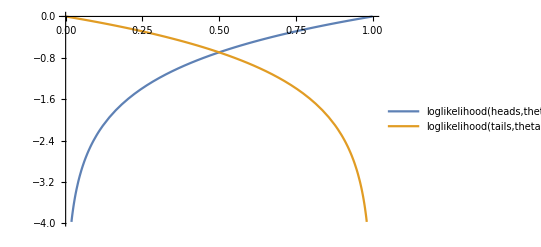

```mathematica
Plot[{loglikelihood[heads, theta], loglikelihood[tails, theta]}, {theta, 0, 1}, PlotLegends->"Expressions"]
```

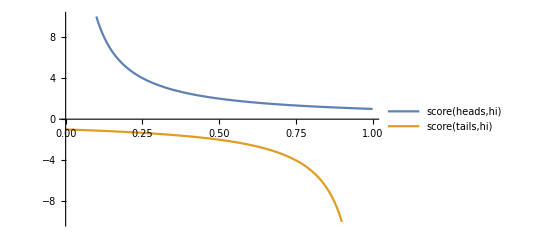

```mathematica
Plot[{score[heads, hi], score[tails, hi]}, {hi, 0, 1}, PlotLegends->"Expressions", PlotRange->{-10, 10}]
```

```mathematica
difference[hi_] := Abs[score[heads, hi] - score[tails, hi]]
```

```mathematica
variance[hi_] := Variance[{score[heads, hi], score[tails, hi]}]
```

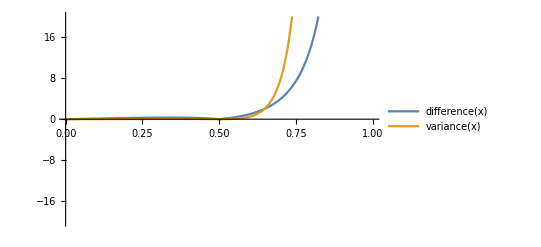

```mathematica
Plot[{difference[x], variance[x]}, {x, 0 ,1}, PlotLegends->"Expressions", PlotRange->{-20, 20}]
```

```mathematica
difference[0.2]
```

6.25

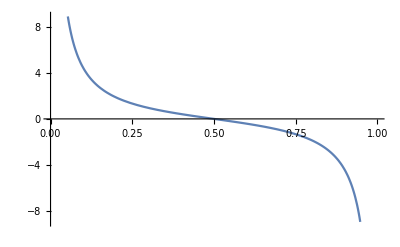

```mathematica
Plot[(1/x + ((-1)/(-x+1)))/2, {x, 0 ,1}]
```

```mathematica
entropy[theta_] := -(1 - theta) * Log[1 - theta] - theta * Log[theta]
```

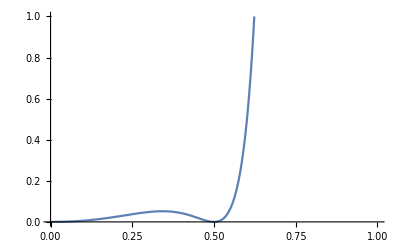

```mathematica
Plot[{variance[x]}, {x, 0 ,1}, PlotLegends->"Expressions", PlotRange->{0, 1}]
```

```mathematica
loglikelihood[heads, 0.5]
```

-0.693147

```mathematica
loglikelihood[tails, 0.5]
```

-0.693147

```mathematica
variance[0.45]
```

8.16243

```mathematica
likelihood[theta_, x_] = theta^x + (1 - theta)^(1-x)
```

(1-theta)^(1-x)+theta^x

```mathematica
Log[D[loglikelihood[theta, x], theta] / likelihood[theta, x]]
```

Log[(-1+2 x)/(((1-theta)^(1-x)+theta^x) ((1-theta) (1-x)+theta x))]